# Point inside Triangle

"THE CHALLENGE"

Write code to determine if a given point in the plane is inside a given triangle.

## More Details

One interior method is listed at Triangle Interior, and another is at Barycentric Coordinates. A third way is to use a  with .

## What Your Code Should Do

Define the function InsideTriangle[{p,q,r},s], where p, q, r are the vertices of a triangle and s is the point to test membership. It should output either True or False, according to whether the point is inside the triangle or not.

You may assume the vertices of the triangle are not collinear.

```mathematica
InsideTriangle[{{5,12},{9,19},{0,13}},{5,15}]
```

True

```mathematica
InsideTriangle[{{5,12},{9,19},{0,13}},{5,12}]
```

True

```mathematica
InsideTriangle[{{5,12},{9,19},{0,13}},{12,17}]
```

False

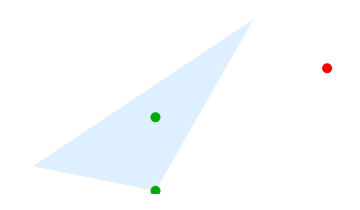

```mathematica
Graphics[{LightBlue,Polygon[{{5,12},{9,19},{0,13}}],PointSize[.02],Darker[Green],Point[{{5,15},{5,12}}],Red,Point[{12,17}]}]
```

"SCRATCH AREA"

"ENTER YOUR CODE HERE"

The required answer seems to be false in the automatic evaluation. I changed the code for it to give the wrong answer as opposed to the correct one given in the descrption: True/False so it come through to you (I have been having same/similar issues with a number of different a lot more complicated challenges!)
(*InsideTriangle[{{p1_,p2_},{q1_,q2_},{r1_,r2_}},{s1_,s2_}]:= RegionMember[Polygon[{{p1, p2}, {q1, q2}, {r1, r2}}], {s1, s2}]*)

```mathematica
InsideTriangle[{{p1_,p2_},{q1_,q2_},{r1_,r2_}},{s1_,s2_}]:= 
RegionMember[Triangle[{{p1, p2}, {q1, q2}, {r1, r2}}], {s1, s2}]
```

```mathematica
InsideTriangle[{{14,7},{18,11},{16,9}},{10,15}]
```

False

```mathematica
InsideTriangle[{{5, 12}, {9, 19}, {0, 13}}, {5, 12}]
```

True